## Problem 4

### Part b

Here, we compute the series expansion for c(k) centered at zero.

```mathematica
Series[Sqrt[g*Tanh[k*h]/k],{k,0,2}]
```

√(g h)-1/6 (h^2 √(g h)) k^2+O[k]^3

## Problem 5

We first compute the exact solution with given initial condition ψ_0.

```mathematica
ψ0[x_]:=Exp[-x^2];
```

```mathematica
a[k_]=Integrate[ψ0[x]*Exp[-I*k*x],{x,-Infinity,Infinity}];
```

```mathematica
ψ[x_,t_]=(1/(2Pi))*Integrate[a[k]*Exp[I*k*x-I*k^2*t],{k,-Infinity,Infinity},Assumptions->t∈Reals&&x∈Reals]
```

(ⅇ^(x^2/(-1-4 ⅈ t)))/(√(1+4 ⅈ t))

Now, we compute the stationary phase approximation for the same given ψ_0.

```mathematica
ψc[x_,t_]=(Exp[I*x^2/(4t)-I*Pi/4]/Sqrt[4*Pi*t])*a[x/(2t)]
```

(ⅇ^(-(ⅈ π)/4-x^2/(16 t^2)+(ⅈ x^2)/(4 t)))/(2 √t)

Finally, we write a function which computes evaluates the integral in our exact formula numerically via Mathematica’s built-in routine.

```mathematica
ψd[x_?NumericQ,t_?NumericQ]:=(1/(2Pi))*NIntegrate[a[k]*Exp[I*k*x-I*k^2*t],{k,-Infinity,Infinity},Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

We now plot all the real and imaginary parts and the modulus of all three solutions against each other on the line x/t=1 on both small and large timescales. Observe that the numerical solution performs well for small t while the stationary phase approximation performs well for large t.

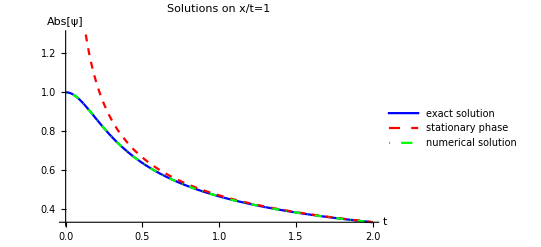

```mathematica
Plot[{Abs[ψ[t,t]],Abs[ψc[t,t]],Abs[ψd[t,t]]},{t,0,2},AxesLabel->{t,Abs[ψ]},PlotLabel->"Solutions on x/t=1",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

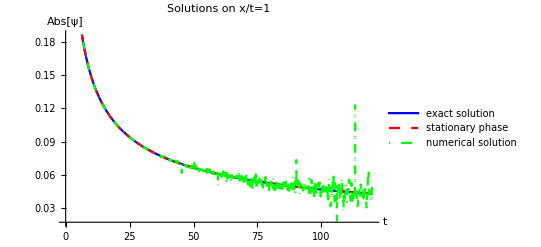

```mathematica
Plot[{Abs[ψ[t,t]],Abs[ψc[t,t]],Abs[ψd[t,t]]},{t,0,120},AxesLabel->{t,Abs[ψ]},PlotLabel->"Solutions on x/t=1",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

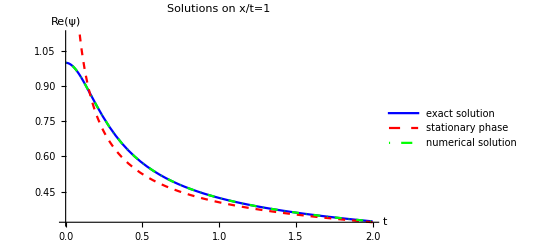

```mathematica
Plot[{Re[ψ[t,t]],Re[ψc[t,t]],Re[ψd[t,t]]},{t,0,2},AxesLabel->{t,Re[ψ]},PlotLabel->"Solutions on x/t=1",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

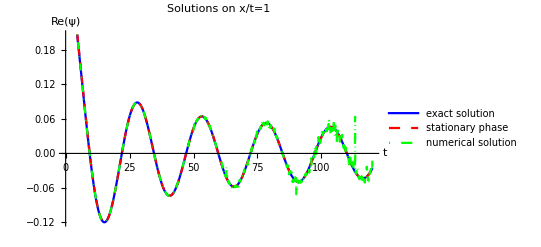

```mathematica
Plot[{Re[ψ[t,t]],Re[ψc[t,t]],Re[ψd[t,t]]},{t,0,120},AxesLabel->{t,Re[ψ]},PlotLabel->"Solutions on x/t=1",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

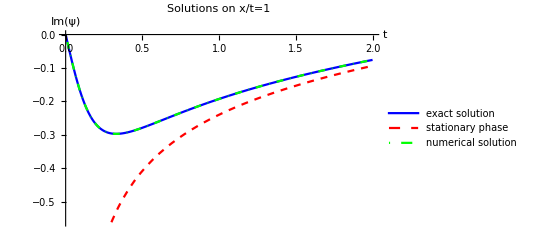

```mathematica
Plot[{Im[ψ[t,t]],Im[ψc[t,t]],Im[ψd[t,t]]},{t,0,2},AxesLabel->{t,Im[ψ]},PlotLabel->"Solutions on x/t=1",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

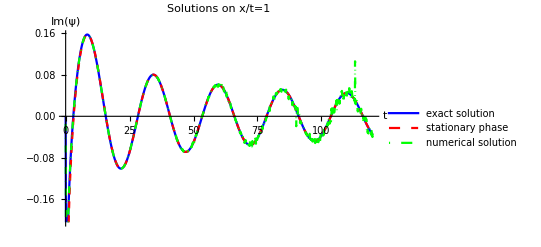

```mathematica
Plot[{Im[ψ[t,t]],Im[ψc[t,t]],Im[ψd[t,t]]},{t,0,120},AxesLabel->{t,Im[ψ]},PlotLabel->"Solutions on x/t=1",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

Now, we plot the various solutions on the line x/t=2 instead and observe similar behavior.

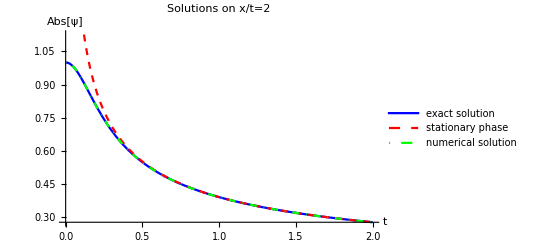

```mathematica
Plot[{Abs[ψ[2t,t]],Abs[ψc[2t,t]],Abs[ψd[2t,t]]},{t,0,2},AxesLabel->{t,Abs[ψ]},PlotLabel->"Solutions on x/t=2",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

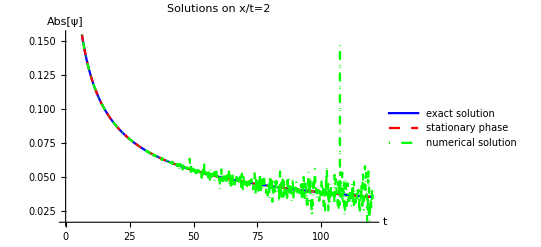

```mathematica
Plot[{Abs[ψ[2t,t]],Abs[ψc[2t,t]],Abs[ψd[2t,t]]},{t,0,120},AxesLabel->{t,Abs[ψ]},PlotLabel->"Solutions on x/t=2",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

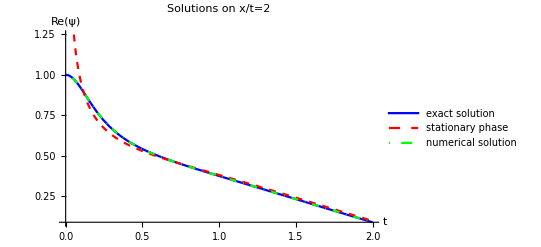

```mathematica
Plot[{Re[ψ[2t,t]],Re[ψc[2t,t]],Re[ψd[2t,t]]},{t,0,2},AxesLabel->{t,Re[ψ]},PlotLabel->"Solutions on x/t=2",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

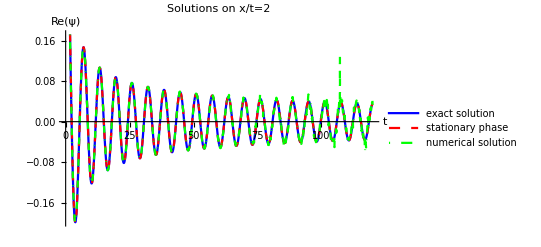

```mathematica
Plot[{Re[ψ[2t,t]],Re[ψc[2t,t]],Re[ψd[2t,t]]},{t,0,120},AxesLabel->{t,Re[ψ]},PlotLabel->"Solutions on x/t=2",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

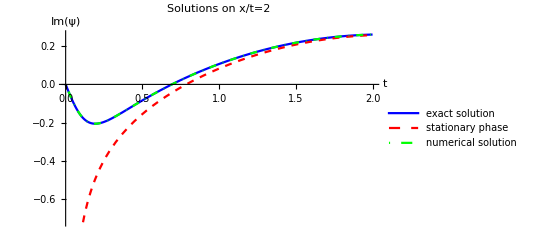

```mathematica
Plot[{Im[ψ[2t,t]],Im[ψc[2t,t]],Im[ψd[2t,t]]},{t,0,2},AxesLabel->{t,Im[ψ]},PlotLabel->"Solutions on x/t=2",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

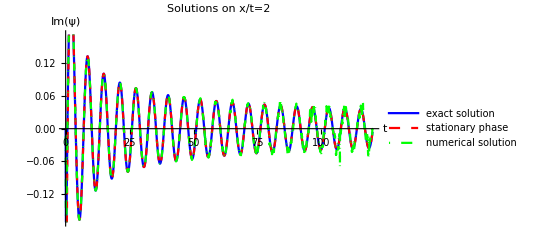

```mathematica
Plot[{Im[ψ[2t,t]],Im[ψc[2t,t]],Im[ψd[2t,t]]},{t,0,120},AxesLabel->{t,Im[ψ]},PlotLabel->"Solutions on x/t=2",PlotLegends->Placed[{"exact solution","stationary phase","numerical solution"},Below],PlotStyle->{Directive[Thick,Blue],Directive[Dashed,Red],Directive[DotDashed,Green]}]
```

## Problem 6

### Part b

Here, we compute the limit of our dispersion relation as h->0.

```mathematica
Limit[-(Exp[I*k*h]-1)^2/(Exp[I*k*h]*h^2),h->0]
```

k^2